# Model Fitting Recap: A Practical Overview for Infectious Disease Modellers

## Sompob Saralamba

## Introduction-What is Model Fitting?

Why do we fit models?

Estimate parameters from observed data

Test hypotheses and compare models

Make predictions and policy decisions

Common model fitting approaches

Least Squares (Optimisation)

Maximum Likelihood Estimation (MLE)

Bayesian Inference (MCMC)

add a simple visual of a data curve vs fitted model

## Example-Fitting an SIR Model

## SIR Model Equations

dS/dt=-β S I
dI/dt=β S I -γ I
dR/dt=γ I

Goal: Estimate β (transmission) & γ (recovery) from epidemic data

Different fitting methods will be demonstrated

include an image of an SIR model curve

Code

```mathematica
Manipulate[
sys={
Susceptibles'[t]==-β Susceptibles[t] Infected[t],
Infected'[t]== β Susceptibles[t]Infected[t]-γ Infected[t],
Recovered'[t]== γ Infected[t]
};

init={Susceptibles[0]==499,Infected[0]==1,Recovered[0]==0};

(*β=0.01;γ=0.1;*)

{sen,inf,rec}=NDSolveValue[sys~Join~init,{Susceptibles[t],Infected[t],
Recovered[t]},{t,0,60}];

Plot[{sen,inf,rec},{t,0,60},Frame->True,
PlotLegends->{"S(t)","I(t)","R(t)"},ImageSize->Medium,
FrameLabel->{"time", "Population"}],

Style["MAEMOD RSE",Italic,FontSize->10],
Style["Simulation of the SIR model",Bold]
,
Delimiter
,{{β,0.002,"β"},0,0.01,0.001,Appearance->"Labeled"},
{{γ,0.3,"γ"},0,1,0.01,Appearance->"Labeled"}
]
```

## Optimization - Based Model Fitting (Least Squares)

### Method: Minimize squared errors between model and data

Solve:

arg min_θ ∑(y_data-y_model)^2

Example: Fit an SIR model to synthetic outbreak data

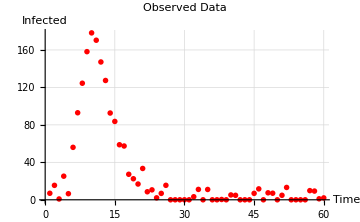

```mathematica
SeedRandom[1234567890];
(* Define the SIR model *)
trueParams = {β -> 0.001, γ -> 0.1};
sys2={
Susceptibles'[t]==-β Susceptibles[t] Infected[t],
Infected'[t]== β Susceptibles[t]Infected[t]-γ Infected[t],
Recovered'[t]== γ Infected[t]
}/.trueParams;

init={Susceptibles[0]==499,Infected[0]==1,Recovered[0]==0};


{sen2,inf2,rec2}=NDSolveValue[sys2~Join~init,{Susceptibles,Infected,
Recovered},{t,0,60}];

(* Generate synthetic epidemic data using true parameters *)
(* Create noisy observations *)
observedData = Table[{t,If[#<0,0,#]&@(inf + 
RandomVariate[NormalDistribution[0, 8]])}, 
{t, 1, 60}];

(* Plot the synthetic data *)
ListPlot[observedData, Joined -> False, PlotStyle -> Red, 
  AxesLabel -> {"Time", "Infected"}, PlotLabel -> "Observed Data",
  ImageSize->Medium,GridLines->Automatic]
```

Code

```mathematica
Clear[LeastSquareFn]
LeastSquareFn[a_?NumericQ,b_?NumericQ]:=Block[{ymod,ydata,sol,infectedSol,params},(*Parameter replacement*)params={beta->a,gamma->b};
(*Solve SIR model*)
sol=NDSolve[{
Susceptibles'[t]==-beta Susceptibles[t] Infected[t],
Infected'[t]==beta Susceptibles[t] Infected[t]-gamma Infected[t],
Recovered'[t]==gamma Infected[t],
(*initial values*)
Susceptibles[0]==499,Infected[0]==1,Recovered[0]==0}/. params,
{Susceptibles,Infected,Recovered},{t,0,60}];

(*Ensure a solution exists*)
infectedSol=Infected/. sol;
If[!ListQ[infectedSol],Return[$Failed]];
(*Generate model predictions*)
ymod=Table[First[infectedSol][ts],{ts,1,60}];

(*Ensure observed data is valid*)
If[!ListQ[observedData]||!MatrixQ[observedData],Return[$Failed]];
ydata=observedData[[All,2]];

(*Compute sum of squared errors*)
Total[(ydata-ymod)^2]
];

estimatedParams=FindMinimum[{LeastSquareFn[β,γ],0<β<0.01,0<γ<0.5},
{{β,0.001},{γ,0.05}}]
```

{2890.58,{β→0.00203328,γ→0.30477}}

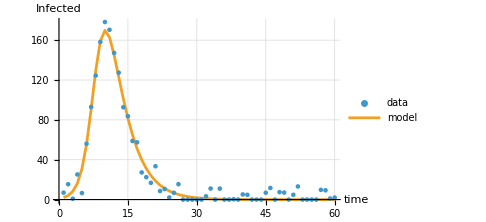

```mathematica
PlotFn[a_?NumericQ,b_?NumericQ]:=Block[{ymod,ydata,sol,infectedSol,params,moddata},(*Parameter replacement*)params={beta->a,gamma->b};
(*Solve SIR model*)
sol=NDSolve[{
Susceptibles'[t]==-beta Susceptibles[t] Infected[t],
Infected'[t]==beta Susceptibles[t] Infected[t]-gamma Infected[t],
Recovered'[t]==gamma Infected[t],
(*initial values*)
Susceptibles[0]==499,Infected[0]==1,Recovered[0]==0}/. params,
{Susceptibles,Infected,Recovered},{t,0,60}];

infectedSol=Infected/. sol;
If[!ListQ[infectedSol],Return[$Failed]];
(*Generate model predictions*)
ymod=Table[First[infectedSol][ts],{ts,1,60}];
moddata=Thread[{Range[1,60],ymod}];

ListPlot[{observedData,moddata},Joined->{False, True},
GridLines->Automatic,PlotLegends->{"data","model"},
AxesLabel->{"time", "Infected"},ImageSize->Medium]
];

PlotFn[β,γ]/.estimatedParams[[2]]
```

## Maximum Likelihood Estimation (MLE)

Likelihood-based approach:

Assumes data follows a known distribution

Finds parameters that maximize the probability of observing the data

Example: Poisson likelihood for incidence data

L(θ)=∏_(i=1)^n P(Y_i|θ)

Demo

MLE assumes observed infection counts follow a probabilistic model (e . g ., normal or Poisson distribution). We define a log - likelihood function, where we assume a normal error model :

log L(β,γ)=∑_(i=1)^n log P(I_obs(t_i)|I_model(t_i))
where
I_obs(t)~N(I_model(t),σ^2)

Code

```mathematica
Clear[logLikelihood]
logLikelihood[a_?NumericQ,b_?NumericQ,sigma_?NumberQ]:=Block[{ymod,ydata,sol,infectedSol,params,residuals},

params={beta->a,gamma->b};

(*Solve SIR model*)
sol=NDSolve[{
Susceptibles'[t]==-beta Susceptibles[t] Infected[t],
Infected'[t]==beta Susceptibles[t] Infected[t]-gamma Infected[t],
Recovered'[t]==gamma Infected[t],

(*initial values*)
Susceptibles[0]==499,Infected[0]==1,Recovered[0]==0}/. params,
{Susceptibles,Infected,Recovered},{t,0,60}];

(*Ensure a solution exists*)
infectedSol=Infected/. sol;
If[!ListQ[infectedSol],Return[$Failed]];

(*Generate model predictions*)
ymod=Table[First[infectedSol][ts],{ts,1,60}];

(*Ensure observed data is valid*)If[!ListQ[observedData]||!MatrixQ[observedData],Return[$Failed]];
ydata=observedData[[All,2]];

residuals=(ydata-ymod);
(*Print[residuals];*)

-Total[(residuals^2)/(2 sigma^2)]
];
```

```mathematica
(* Perform MLE *)
mleResults=FindMaximum[{logLikelihood[β,γ,0.01], 0.0 <β<0.01,0.0<γ<0.2},
{{β,0.001},{γ,0.05}}]
```

{-2.11194×10^8,{β→0.00191548,γ→0.2}}

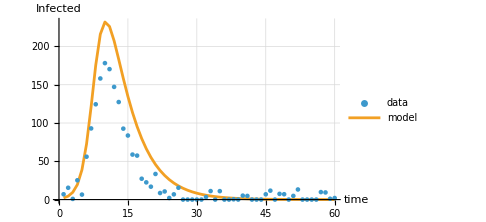

```mathematica
PlotFn[β,γ]/.mleResults[[2]]
```

## Bayesian Model Fitting & MCMC

Why Bayesian?

Incorporates prior knowledge

Provides full posterior distributions (uncertainty estimates)

Running MCMC to estimate β and γ

Code

The code of the examples can be downloaded from